## CASO LINEALMENTE SEPARABLE

```mathematica
puntos1={{1,2},{1,6},{2,3},{0,7},{-1,3},{-0.5,5},{0.5,6},{0,1},{-0.6,8},{0.2,3},{1.3,5},{1.6,6.5},{-0.3,6},{0.4,1},{1.1,7.3},{1.8,3.4},{0.7,5},{-0.3,2},{1.5,2}}
```

{{1,2},{1,6},{2,3},{0,7},{-1,3},{-0.5,5},{0.5,6},{0,1},{-0.6,8},{0.2,3},{1.3,5},{1.6,6.5},{-0.3,6},{0.4,1},{1.1,7.3},{1.8,3.4},{0.7,5},{-0.3,2},{1.5,2}}

```mathematica
puntos2={{6,1},{5.5,1.2},{7,2},{8,6},{6.6,8},{9,2},{7,7},{8.5,4},{4.9,5},{7.7,3},{6.2,4.7},{8.2,8},{8.8,5.3},{6.5,2},{5.4,6.7},{7.2,4},{5.7,3.2},{4,0.5}}
```

{{6,1},{5.5,1.2},{7,2},{8,6},{6.6,8},{9,2},{7,7},{8.5,4},{4.9,5},{7.7,3},{6.2,4.7},{8.2,8},{8.8,5.3},{6.5,2},{5.4,6.7},{7.2,4},{5.7,3.2},{4,0.5}}

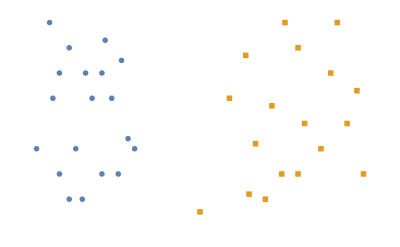

```mathematica
f=ListPlot[{puntos1,puntos2},Axes->False,PlotMarkers->{✶,■}]
```

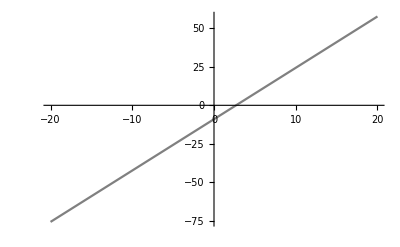

```mathematica
g1=Plot[(-2.7+x)/0.3,{x,-20,20},PlotStyle->Gray]
```

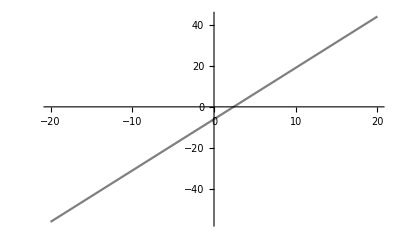

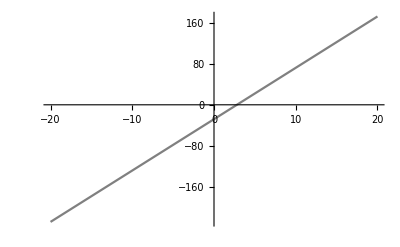

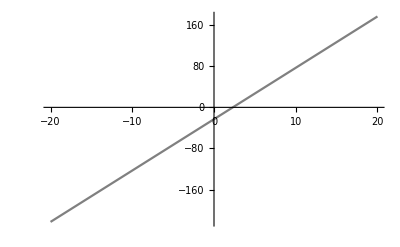

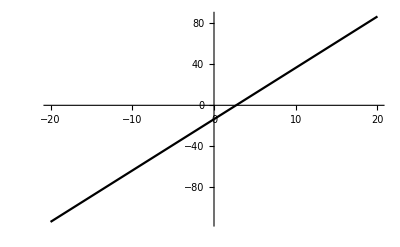

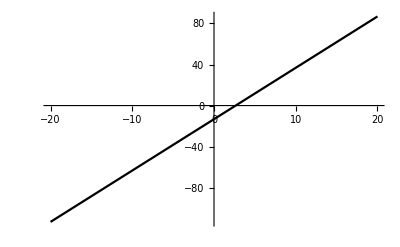

```mathematica
g2=Plot[(-2.4+x)/0.4,{x,-20,20},PlotStyle->Gray]
g3=Plot[(-2.8+x)/0.1,{x,-20,20},PlotStyle->Gray]
g4=Plot[(-2.3+x)/0.1,{x,-20,20},PlotStyle->Gray]
gf=Plot[5.004494991540595*x-13.264159063448506,{x,-20,20},PlotStyle->Black] (*COMENTARIO: Es la función del hiperplano separador *)
```

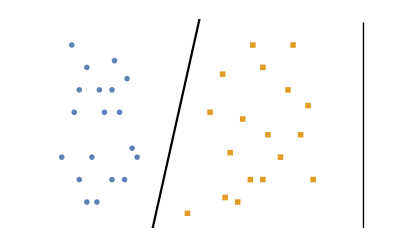

```mathematica
Show[f,gf,Epilog->Line[{{11,-2},{11,9}}],PlotRange->{{-2,11},{0,9}}]
```

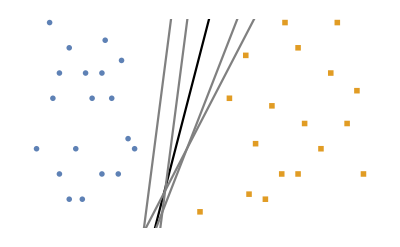

```mathematica
Show[f,gf,g1,g2,g3,g4]
```

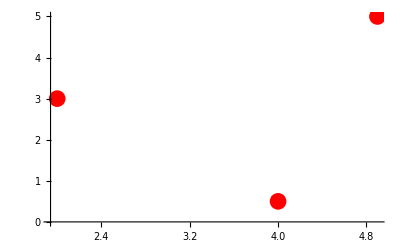

```mathematica
p=ListPlot[{{2,3},{4.9,5},{4,0.5}},PlotStyle->{Red,PointSize[0.03]}]
```

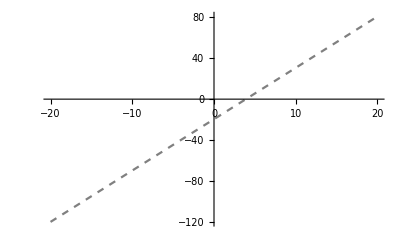

```mathematica
h=Plot[-19.522025458548917+5.004494991540595*x,{x,-20,20},PlotStyle->{Dashed,Gray}]
```

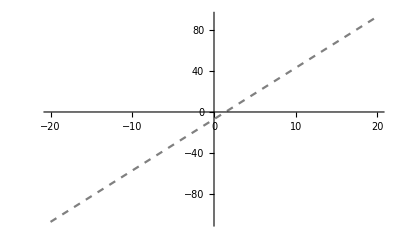

```mathematica
k=Plot[-7.0089899830811895+5.004494991540595*x,{x,-20,20},PlotStyle->{Dashed,Gray}]
```

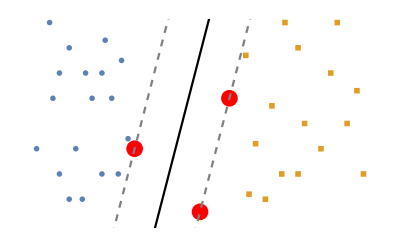

```mathematica
Show[f,gf,p,h,k]
```

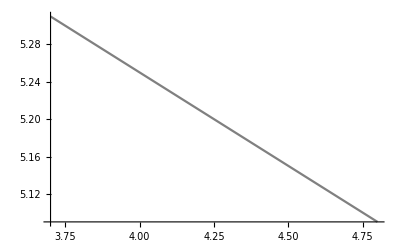

```mathematica
M=Plot[6.05-0.2x,{x,3.7,4.8},PlotStyle->Gray]
```

Creo que lo de abajo no sirve para nada

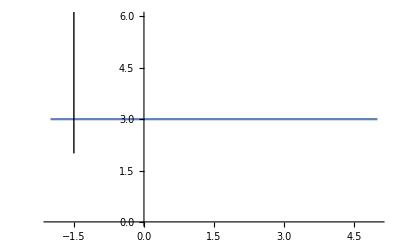

```mathematica
H=Plot[3,{x,-2,5},Epilog->Line[{{-1.5,2},{-1.5,9}}]]
```

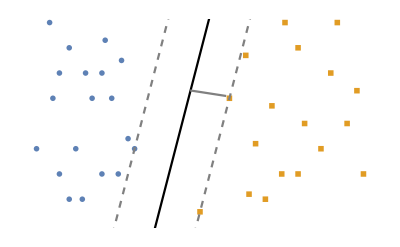

```mathematica
Show[f,gf,h,k,M,Epilog->Inset[Graphics[{Black,Text[Style[τ,16]]}]]]
```

## CASO CUASI - SEPARABLE

```mathematica
Clear[f,g,h,k]
```

```mathematica
puntos3={{1,2},{1,6},{2,3},{0,7},{-1,3},{-0.5,5},{0.5,6},{0,1},{-0.6,8},{0.2,3},{1.3,5},{1.6,6.5},{-0.3,6},{0.4,1},{1.1,7.3},{1.8,3.4},{0.7,5},{-0.3,2},{2,6},{2.3,7},{1.5,2},{4.5,6.9},{2.6,4}}
```

{{1,2},{1,6},{2,3},{0,7},{-1,3},{-0.5,5},{0.5,6},{0,1},{-0.6,8},{0.2,3},{1.3,5},{1.6,6.5},{-0.3,6},{0.4,1},{1.1,7.3},{1.8,3.4},{0.7,5},{-0.3,2},{2,6},{2.3,7},{1.5,2},{4.5,6.9},{2.6,4}}

```mathematica
{2.6,4}
```

{2.6,4}

```mathematica
puntos4={{6,1},{5.5,1.2},{7,2},{8,6},{6.6,8},{9,2},{7,7},{8.5,4},{2,5},{7.7,3},{6.2,4.7},{8.2,8},{8.8,5.3},{6.5,2},{7.2,4},{5.6,6.7},{5.7,3.2},{5,0.5},{3.5,1.2},{4.7,2.7}}
```

{{6,1},{5.5,1.2},{7,2},{8,6},{6.6,8},{9,2},{7,7},{8.5,4},{2,5},{7.7,3},{6.2,4.7},{8.2,8},{8.8,5.3},{6.5,2},{7.2,4},{5.6,6.7},{5.7,3.2},{4,0.5},{2.5,1.2},{3.7,2.7}}

```mathematica
{3.7,2.7}
```

{3.7,2.7}

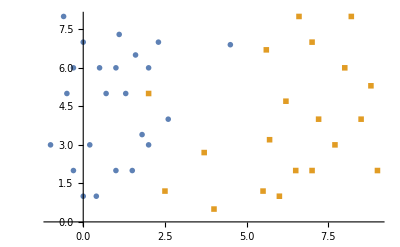

```mathematica
f=ListPlot[{puntos3,puntos4},PlotMarkers->{✶,■},Axes->True]
```

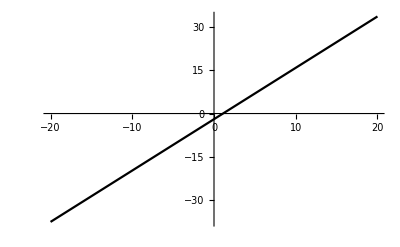

```mathematica
g=Plot[1.7741934410914781*x-1.9482917291139037,{x,-20,20},PlotStyle->Black]
```

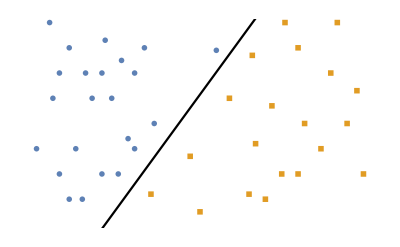

```mathematica
Show[f,g]
```

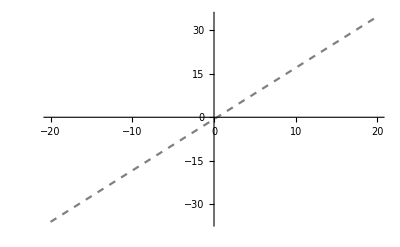

```mathematica
k=Plot[-0.6612901616372171+1.7741934410914781*x,{x,-20,20},PlotStyle->{Dashed,Gray}]
```

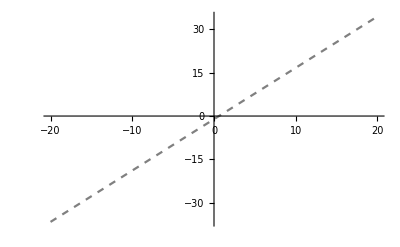

```mathematica
h=Plot[-1.0838704849116514+1.7741934410914781*x,{x,-20,20},PlotStyle->{Dashed,Gray}]
```

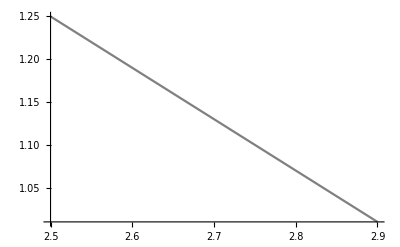

```mathematica
s1=Plot[2.75-0.6x,{x,2.5,2.9},PlotStyle->Gray]
```

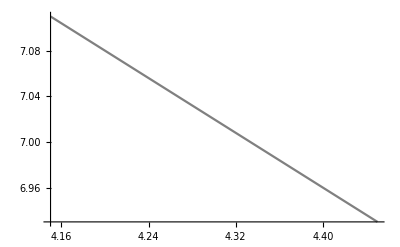

```mathematica
s2=Plot[9.6-0.6x,{x,4.15,4.45},PlotStyle->Gray]
```

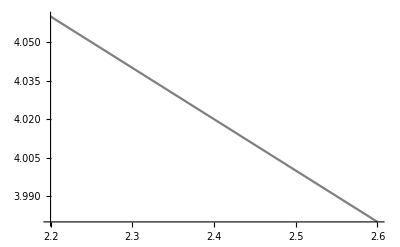

```mathematica
s3=Plot[4.5-0.2x,{x,2.2,2.6},PlotStyle->Gray]
```

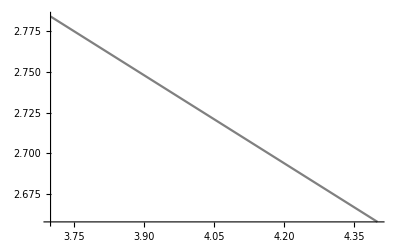

```mathematica
s4=Plot[3.45-0.18x,{x,3.7,4.4},PlotStyle->Gray]
```

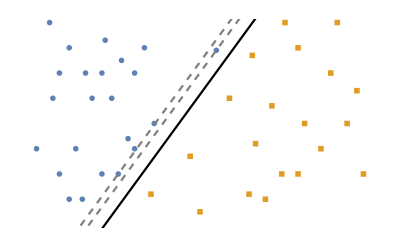

```mathematica
Show[f,g,h,k]
```

```mathematica
Line[{{-1.5,-3},{-1.5,10}}],
```

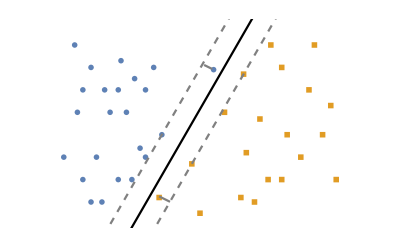

```mathematica
Show[f,g,h,k,s1,s2,Axes->False,PlotRange->{{-2,10},{0,9}},Epilog->Inset[Graphics[{Black,Text[Style[Subscript[ϵ, i],12]]}]]]
```

## CASO NO SEPARABLE LINEALMENTE

```mathematica
Clear[f,g,h,k]
```

```mathematica
puntos5={{0,0},{1,4},{4,20},{2,12},{-2,6},{1.2,16},{1.5,-2},{-3,30},{-2.3,14},{3.4,8},{1.7,2},{1.3,24},{1,0.2},{-1.5,12},{-3.7,24},{0.1,10},{-1,18},{-2.5,22},{2.5,28},{0,26},{2.7,16},{-0.7,4}}
```

{{0,0},{1,4},{4,20},{2,12},{-2,6},{1.2,16},{1.5,-2},{-3,30},{-2.3,14},{3.4,8},{1.7,2},{1.3,24},{1,0.2},{-1.5,12},{-3.7,24},{0.1,10},{-1,18},{-2.5,22},{2.5,28},{0,26},{2.7,16},{-0.7,4}}

```mathematica
puntos6={{-1,-5},{-2,1},{3,-3},{4,5},{-4,13},{-3,-3},{1.5,-7},{-3.4,5},{-5,25},{3.5,-5},{0.5,-7},{4.5,-1},{5,-11},{4.8,9},{-5,3},{-3.8,-5},{-1.5,-7},{-4.5,7},{2.5,-11},{-4.7,17},{-0.2,-11},{-5.2,-9},{2.5,-3}}
```

{{-1,-5},{-2,1},{3,-3},{4,5},{-4,13},{-3,-3},{1.5,-7},{-3.4,5},{-5,25},{3.5,-5},{0.5,-7},{4.5,-1},{5,-11},{4.8,9},{-5,3},{-3.8,-5},{-1.5,-7},{-4.5,7},{2.5,-11},{-4.7,17},{-0.2,-11},{-5.2,-9},{2.5,-3}}

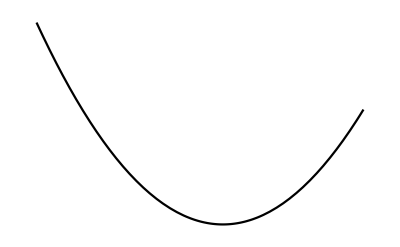

```mathematica
f=Plot[x^2-1.4x-3,{x,-5,5},PlotStyle->Black,Axes->False]
```

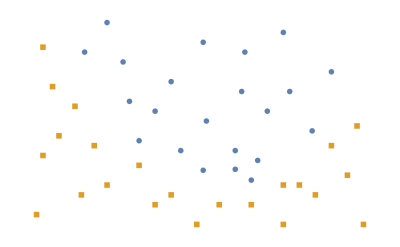

```mathematica
g=ListPlot[{puntos5,puntos6},PlotMarkers->{✶,■},Axes->False]
```

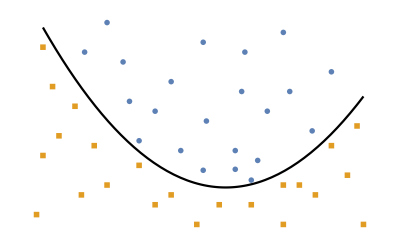

```mathematica
Show[f,g,PlotRange->All]
```

la transformación es si la segunda componente es par o si el reto de dividir entre 2 es 0 entonces la tercera componente es un 3 y en caso contrario un - 3

```mathematica
puntos5t={{0,0,3},{1,4,3},{4,20,3},{2,12,3},{-2,6,3},{1.2,16,3},{1.5,-2,3},{-3,30,3},{-2.3,14,3},{3.4,8,3},{1.7,2,3},{1.3,24,3},{1,0.2,3},{-1.5,12,3},{-3.7,24,3},{0.1,10,3},{-1,18,3},{-2.5,22,3},{2.5,28,3},{0,26,3},{2.7,16,3},{-0.7,4,3}}
```

{{0,0,3},{1,4,3},{4,20,3},{2,12,3},{-2,6,3},{1.2,16,3},{1.5,-2,3},{-3,30,3},{-2.3,14,3},{3.4,8,3},{1.7,2,3},{1.3,24,3},{1,0.2,3},{-1.5,12,3},{-3.7,24,3},{0.1,10,3},{-1,18,3},{-2.5,22,3},{2.5,28,3},{0,26,3},{2.7,16,3},{-0.7,4,3}}

```mathematica
puntos6t={{-1,-5,-3},{-2,1,-3},{3,-3,-3},{4,5,-3},{-4,13,-3},{-3,-3,-3},{1.5,-7,-3},{-3.4,5,-3},{-5,25,-3},{3.5,-5,-3},{0.5,-8,-3},{4.5,-1,-3},{5,-11,-3},{4.8,9,-3},{-5,3,-3},{-3.8,-5,-3},{-1.5,-7,-3},{-4.5,7,-3},{2.5,-11,-3},{-4.7,17,-3},{-0.2,-11,-3},{-5.2,-9,-3},{2.5,-3,-3}}
```

{{-1,-5,-3},{-2,1,-3},{3,-3,-3},{4,5,-3},{-4,13,-3},{-3,-3,-3},{1.5,-7,-3},{-3.4,5,-3},{-5,25,-3},{3.5,-5,-3},{0.5,-8,-3},{4.5,-1,-3},{5,-11,-3},{4.8,9,-3},{-5,3,-3},{-3.8,-5,-3},{-1.5,-7,-3},{-4.5,7,-3},{2.5,-11,-3},{-4.7,17,-3},{-0.2,-11,-3},{-5.2,-9,-3},{2.5,-3,-3}}

```mathematica
h=ListPointPlot3D[{puntos5t,puntos6t},Axes->False,PlotRange->{{-6,6},{-15,30},{-4,4}}]
```

-Graphics3D-

```mathematica
k=Plot3D[0,{x,-20,20},{y,-20,30},PlotStyle->Black]
```

-Graphics3D-

```mathematica
Show[h,k,PlotRange->{{-6,6},{-15,30},{-4,4}},Axes->False]
```

-Graphics3D-

## SVM - MULTICLASE

```mathematica
Clear[f,g1,g2,g3,h1,h2,h3,k,k1,k2,k3,k4]
```

## OVO

```mathematica
puntos7={{-5,4},{-4,-2},{-4.5,3},{-3,1},{-3.5,2.5},{-5.5,-1},{-4.2,0.5},{-3.7,3},{-4.7,-3},{-4.8,1.6},{-3.3,-1},{-4.6,5},{-6,2}}
```

{{-5,4},{-4,-2},{-4.5,3},{-3,1},{-3.5,2.5},{-5.5,-1},{-4.2,0.5},{-3.7,3},{-4.7,-3},{-4.8,1.6},{-3.3,-1},{-4.6,5},{-6,2}}

```mathematica
puntos8={{0,11},{-2,7},{-0.7,10},{-3,8},{-3.5,10.3},{-2,9},{1,10},{1.7,9.3},{1.5,8.3},{2,7.7},{-1.5,10.5},{0.5,10},{0.3,8},{-1,8.7},{-2.4,12}}
```

{{0,11},{-2,7},{-0.7,10},{-3,8},{-3.5,10.3},{-2,9},{1,10},{1.7,9.3},{1.5,8.3},{2,7.7},{-1.5,10.5},{0.5,10},{0.3,8},{-1,8.7},{-2.4,12}}

```mathematica
puntos9={{2,-2},{3,3},{2.4,-0.5},{4,2.2},{3.2,1},{3.5,-2.5},{4.3,4.3},{4,-4},{5,0},{5.3,2},{5.2,-1.6},{3.7,0},{2,1},{3,-3.2}}
```

{{2,-2},{3,3},{2.4,-0.5},{4,2.2},{3.2,1},{3.5,-2.5},{4.3,4.3},{4,-4},{5,0},{5.3,2},{5.2,-1.6},{3.7,0},{2,1},{3,-3.2}}

```mathematica
puntos10={{-0.7,-5.5}}
```

{{-0.7,-5.5}}

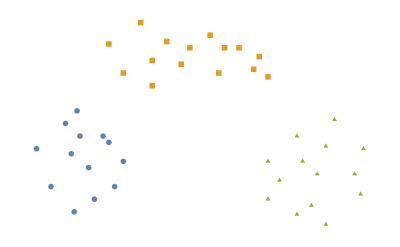

```mathematica
f2=ListPlot[{puntos7,puntos8,puntos9},Axes->False,PlotMarkers->{✶,■,▲}]
```

```mathematica
f1=ListPlot[puntos10,PlotMarkers->◆,PlotStyle->111,Axes->False]
```

-Graphics-

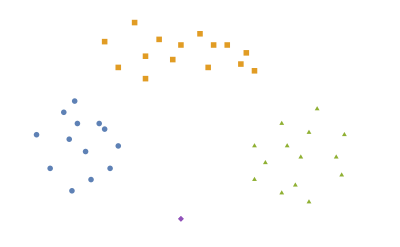

```mathematica
f=Show[f2,f1,PlotRange->{{-6,6},{-6,12}}]
```

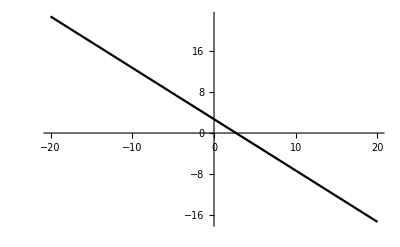

```mathematica
g1=Plot[2.6989649520944354-1.0002985843057266*x,{x,-20,20},PlotStyle->Black]
```

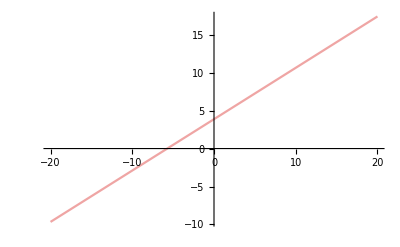

```mathematica
g2=Plot[3.869117849013384+x*0.676470588235294,{x,-20,20},PlotStyle->9]
```

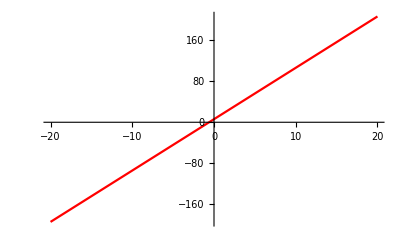

```mathematica
g3=Plot[(0.6+x)/0.1,{x,-20,20},PlotStyle->Red]
```

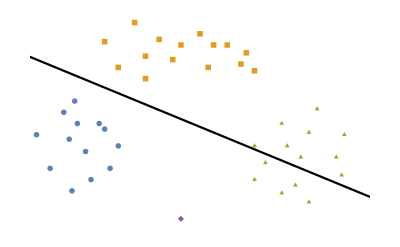

```mathematica
Show[f,g1]
```

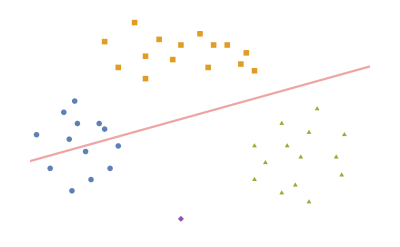

```mathematica
Show[f,g2]
```

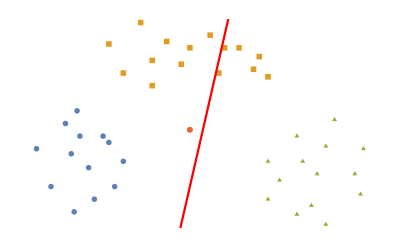

```mathematica
Show[f,g3] (*ESTA NO ME FUNCIONA, PORQUE SEGURO QUE ME DA UNA LINEA VERTICAL*)
```

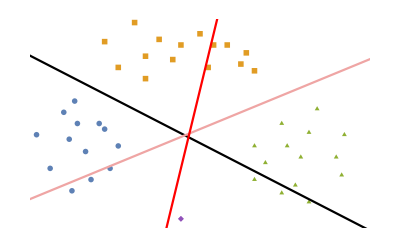

```mathematica
Show[f,g1,g2,g3]
```

```mathematica
(*puedo hacer que pasen las tres por el mismo sitio, pero no lo veo necesario, pero si lo preferís lo puedo cambiar*)
```

Show::gcomb: Could not combine the graphics objects in ….

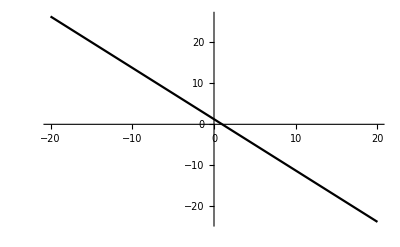
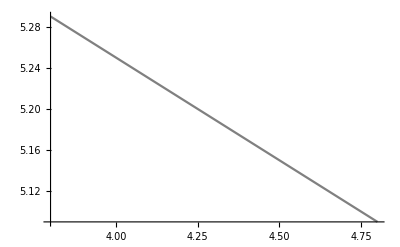
Show[-Graphics-,-Graphics-,-Graphics3D-,k,-Graphics-,Epilog→Inset[-Graphics-]]

```mathematica
Show[f,g1,h,k,M,Epilog->Inset[Graphics[{Black,Text[Style[(▲✶),10]]}]]]
```

## OVA

```mathematica
puntos7={{-5,4},{-4,-2},{-4.5,3},{-3,1},{-3.5,2.5},{-5.5,-1},{-4.2,0.5},{-3.7,3},{-4.7,-3},{-4.8,1.6},{-3.3,-1},{-4.6,5},{-6,2}}
```

{{-5,4},{-4,-2},{-4.5,3},{-3,1},{-3.5,2.5},{-5.5,-1},{-4.2,0.5},{-3.7,3},{-4.7,-3},{-4.8,1.6},{-3.3,-1},{-4.6,5},{-6,2}}

```mathematica
puntos8={{0,11},{-2,7},{-0.7,10},{-3,8},{-3.5,10.3},{-2,9},{1,10},{1.7,9.3},{1.5,8.3},{2,7.7},{-1.5,10.5},{0.5,10},{0.3,8},{-1,8.7},{-2.4,12}}
```

{{0,11},{-2,7},{-0.7,10},{-3,8},{-3.5,10.3},{-2,9},{1,10},{1.7,9.3},{1.5,8.3},{2,7.7},{-1.5,10.5},{0.5,10},{0.3,8},{-1,8.7},{-2.4,12}}

```mathematica
puntos9={{2,-2},{3,3},{2.4,-0.5},{4,2.2},{3.2,1},{3.5,-2.5},{4.3,4.3},{4,-4},{5,0},{5.3,2},{5.2,-1.6},{3.7,0},{2,1},{3,-3.2}}
```

{{2,-2},{3,3},{2.4,-0.5},{4,2.2},{3.2,1},{3.5,-2.5},{4.3,4.3},{4,-4},{5,0},{5.3,2},{5.2,-1.6},{3.7,0},{2,1},{3,-3.2}}

```mathematica
puntos10={{-0.7,3.5}}
```

{{-0.7,3.5}}

```mathematica
f1=ListPlot[{puntos7,puntos8,puntos9},Axes->False,PlotMarkers->{✶,■,▲}]
```

-Graphics-

```mathematica
f2=ListPlot[puntos10,PlotMarkers->◆,PlotStyle->111,Axes->False]
```

-Graphics-

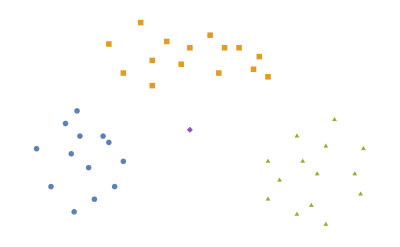

```mathematica
f=Show[f1,f2]
```

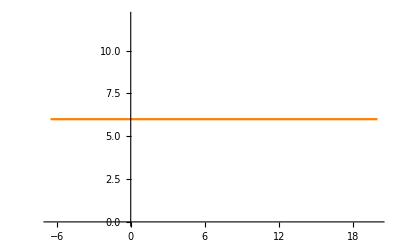

```mathematica
h1=Plot[6,{x,-6.5,20},PlotStyle->Orange]
```

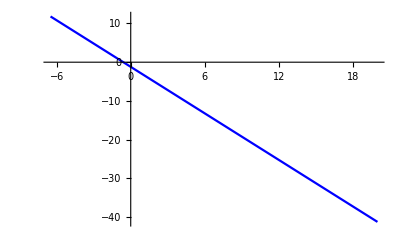

```mathematica
h2=Plot[(-0.6-x)/0.5,{x,-6.5,20},PlotStyle->Blue]
```

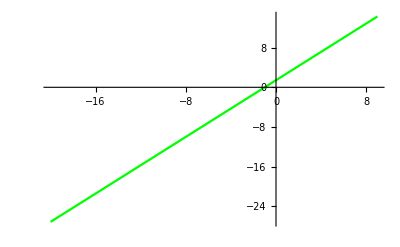

```mathematica
h3=Plot[(1+x)/0.7,{x,-20,9},PlotStyle->Green]
```

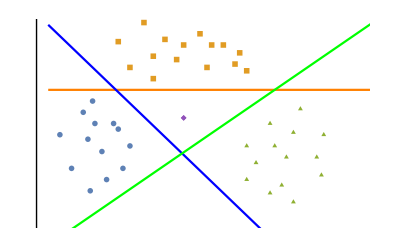

```mathematica
Show[f,h1,h2,h3,Epilog->Line[{{-7,-9},{-7,13}}],PlotRange->{{-7,7},{-6,12}}]
```

## DAGSVM

```mathematica
puntos7={{-5,4},{-4,-2},{-4.5,3},{-3,1},{-3.5,2.5},{-5.5,-1},{-4.2,0.5},{-3.7,3},{-4.7,-3},{-4.8,1.6},{-3.3,-1},{-4.6,5},{-6,2}}
```

{{-5,4},{-4,-2},{-4.5,3},{-3,1},{-3.5,2.5},{-5.5,-1},{-4.2,0.5},{-3.7,3},{-4.7,-3},{-4.8,1.6},{-3.3,-1},{-4.6,5},{-6,2}}

```mathematica
puntos8={{0,11},{-2,7},{-0.7,10},{-3,8},{-3.5,10.3},{-2,9},{1,10},{1.7,9.3},{1.5,8.3},{2,7.7},{-1.5,10.5},{0.5,10},{0.3,8},{-1,8.7},{-2.4,12}}
```

{{0,11},{-2,7},{-0.7,10},{-3,8},{-3.5,10.3},{-2,9},{1,10},{1.7,9.3},{1.5,8.3},{2,7.7},{-1.5,10.5},{0.5,10},{0.3,8},{-1,8.7},{-2.4,12}}

```mathematica
puntos9={{2,-2},{3,3},{2.4,-0.5},{4,2.2},{3.2,1},{3.5,-2.5},{4.3,4.3},{4,-4},{5,0},{5.3,2},{5.2,-1.6},{3.7,0},{2,1},{3,-3.2}}
```

{{2,-2},{3,3},{2.4,-0.5},{4,2.2},{3.2,1},{3.5,-2.5},{4.3,4.3},{4,-4},{5,0},{5.3,2},{5.2,-1.6},{3.7,0},{2,1},{3,-3.2}}

sube dos para arriba en los puntos de abajo,  para tener los puntos originales

```mathematica
puntos10={{0,-9},{-1.5,-10},{2,-12},{-0.5,-11},{0.6,-9.5},{2.5,-13},{1.6,-12.7},{-1.3,-14},{-2.6,-13.2},{0.75,-13.6},{0,-16},{-2.2,-14},{1.8,-15.7},{-1,-18}}
```

{{0,-9},{-1.5,-10},{2,-12},{-0.5,-11},{0.6,-9.5},{2.5,-13},{1.6,-12.7},{-1.3,-14},{-2.6,-13.2},{0.75,-13.6},{0,-16},{-2.2,-14},{1.8,-15.7},{-1,-18}}

```mathematica
puntos11={{-1.8,-4}}
```

{{-1.8,-4}}

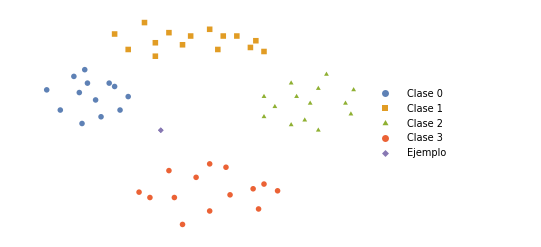

```mathematica
k=ListPlot[{puntos7,puntos8,puntos9,puntos10,puntos11},Axes->False,PlotMarkers->{✶,■,▲,●,◆},PlotLegends->{"Clase 0","Clase 1","Clase 2","Clase 3","Ejemplo"}]
```

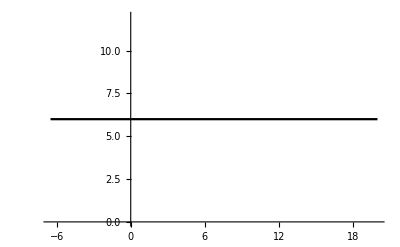

```mathematica
k1=Plot[6,{x,-6.5,20},PlotStyle->Black]
```

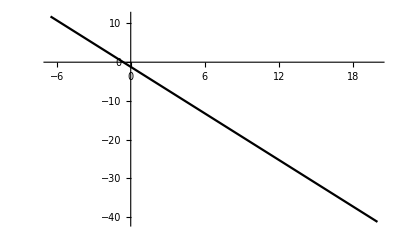

```mathematica
k2=Plot[(-0.6-x)/0.5,{x,-6.5,20},PlotStyle->Black]
```

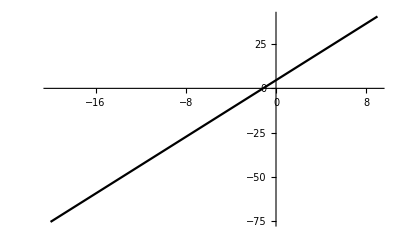

```mathematica
k3=Plot[(1.15+x)/0.25,{x,-20,9},PlotStyle->Black]
```

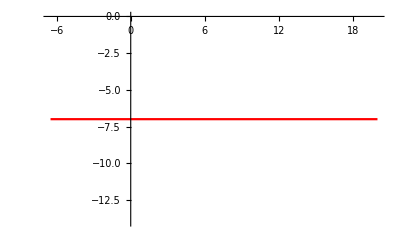

```mathematica
k4=Plot[-7,{x,-6.5,20},PlotStyle->Red]
```

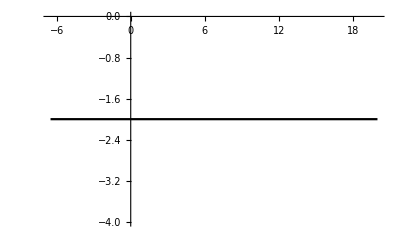

```mathematica
k5=Plot[-2,{x,-6.5,20},PlotStyle->Black]
```

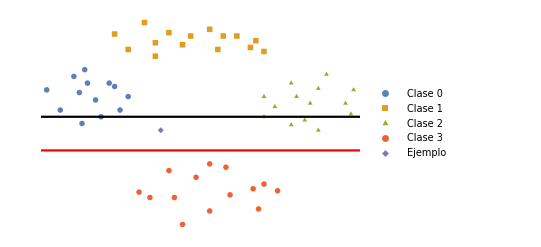

```mathematica
Show[k,k5,k4]
```

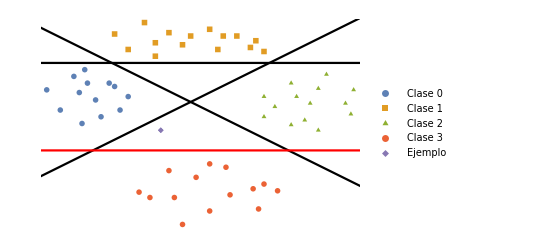

```mathematica
Show[k,k1,k2,k3,k4,Epilog->Line[{{-7,-9},{-7,13}}]]
```

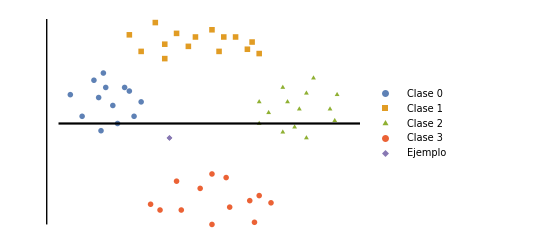

```mathematica
Show[k,k5,Epilog->Line[{{-7,-16},{-7,16}}], PlotRange->{{-7,6},{-16,12}}]
```

Separa las clases 0 - 3

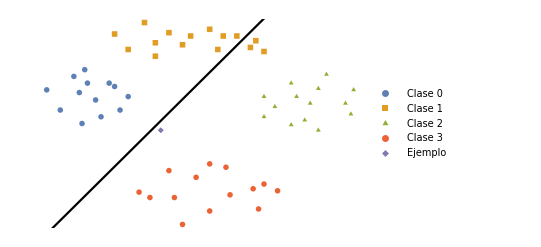

```mathematica
Show[k,k3]
```

Separa las clases 1 - 3

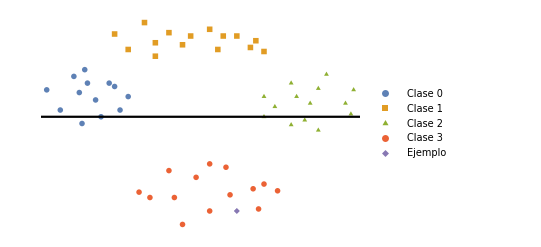

```mathematica
Show[k,k5]
```

Separa las clases 2 - 3

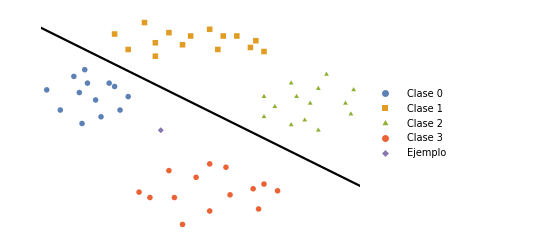

```mathematica
Show[k,k2]
```

## DAGSVM LISTA 1

```mathematica
puntos7={{-4,5},{-3,-1},{-3.5,4},{-2.6,2},{-2.5,3.5},{-4.5,2},{-3.2,1.5},{-2.7,4},{-3.7,0},{-3.8,2.6}}
```

{{-4,5},{-3,-1},{-3.5,4},{-2.6,2},{-2.5,3.5},{-4.5,2},{-3.2,1.5},{-2.7,4},{-3.7,0},{-3.8,2.6}}

```mathematica
puntos8={{0,13},{-0.5,9},{-0.4,12},{-1,10},{-1.5,12.3},{-1.3,11},{0.3,10.5},{1.4,11.3},{0.1,9.6},{0.8,9.7},{-0.7,12.5},{0.5,12}}
```

{{0,13},{-0.5,9},{-0.4,12},{-1,10},{-1.5,12.3},{-1.3,11},{0.3,10.5},{1.4,11.3},{0.1,9.6},{0.8,9.7},{-0.7,12.5},{0.5,12}}

```mathematica
puntos9={{-1,-6},{-1,-2},{-1.4,-5.5},{0,-3.2},{-1.2,-4},{-1.5,-6.5},{0.3,-2.3},{0,-7},{0,-4},{0.5,-3},{0.2,-5.6}}
```

{{-1,-6},{-1,-2},{-1.4,-5.5},{0,-3.2},{-1.2,-4},{-1.5,-6.5},{0.3,-2.3},{0,-7},{0,-4},{0.5,-3},{0.2,-5.6}}

```mathematica
puntos10={{}}
```

{{}}

```mathematica
puntos11={{-1.5,1}}
```

{{-1.5,1}}

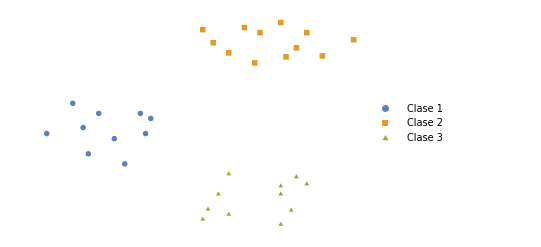

```mathematica
k1=ListPlot[{puntos7,puntos8,puntos9},Axes->False,PlotMarkers->{✶,■,▲},PlotLegends->{"Clase 1","Clase 2","Clase 3"}]
```

```mathematica
k2=ListPlot[puntos11,Axes->False,PlotMarkers->◆,PlotStyle->111,PlotLegends->{"Ejemplo"}]
```

-Graphics-

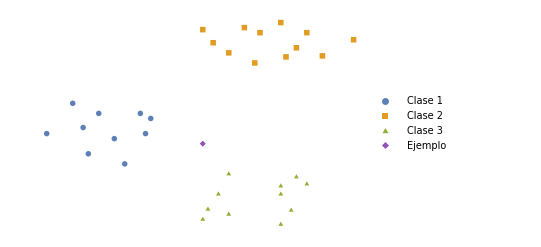

```mathematica
k=Show[k1,k2]
```

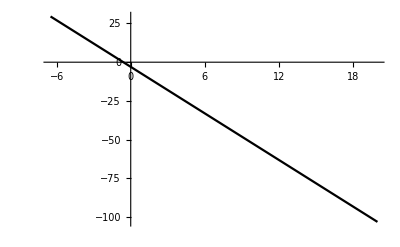

```mathematica
h1=Plot[(-0.6-x)/0.2,{x,-6.5,20},PlotStyle->Black]
```

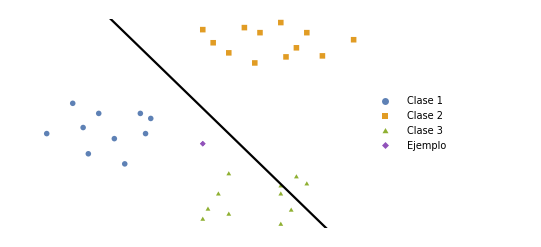

```mathematica
Show[k,h1]
```

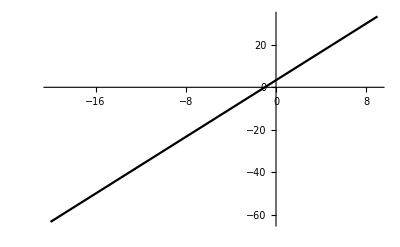

```mathematica
h2=Plot[(1+x)/0.3,{x,-20,9},PlotStyle->Black]
```

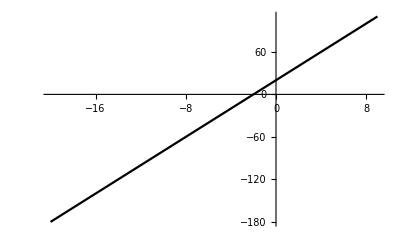

```mathematica
h3=Plot[(2+x)/0.1,{x,-20,9},PlotStyle->Black]
```

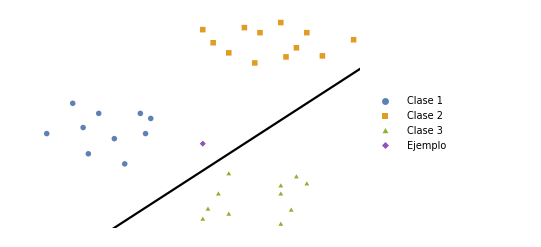

```mathematica
Show[k,h2]
```

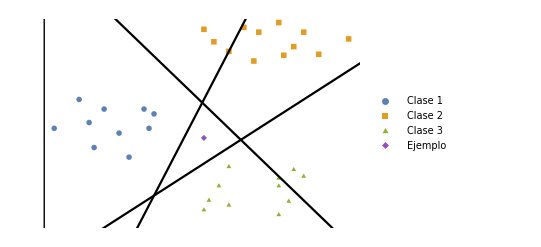

```mathematica
Show[k,h1,h2,h3,Epilog->Line[{{-4.7,-16},{-4.7,16}}],PlotRange->{{-4.65,1.5},{-8,13}}]
```

## DAGSVM LISTA 2

```mathematica
puntos7={{-5,4},{-4,-2},{-4.5,3},{-3,1},{-3.5,2.5},{-5.5,-1},{-4.2,0.5},{-3.7,3},{-4.7,-3},{-4.8,1.6},{-3.3,-1},{-4.6,5},{-6,2}}
```

```mathematica
puntos7={{-5,4},{-4,-2},{-4.5,3},{-3,1},{-3.5,2.5},{-5.5,-1},{-4.2,0.5},{-3.7,3},{-4.7,-3},{-4.8,1.6},{-3.3,-1},{-4.6,5},{-6,2}}
```

```mathematica
puntos7={{-5,4},{-4,-2},{-4.5,3},{-3,1},{-3.5,2.5},{-5.5,-1},{-4.2,0.5},{-3.7,3},{-4.7,-3},{-4.8,1.6},{-3.3,-1},{-4.6,5},{-6,2}}
```

```mathematica
k=ListPlot[{puntos7,puntos8,puntos9,puntos10,puntos11},Axes->False,PlotMarkers->{✶,■,▲,●,◆},PlotLegends->{"Clase 0","Clase 1","Clase 2","Clase 3","Ejemplo"}]
```